# Make a Maxwell-Boltzmann distribution of the kappa dists

Data options

```mathematica
EarlyOrLate="Early";
BeamNoBeam = "Beam";
```

### 2018/05/10 data

```mathematica
kHistEarlyReq={{1.88,20.00},{2.62,138.00},{3.38,129.00},{4.12,97.00},{4.88,100.00},{5.62,79.00},{6.38,57.00},{7.12,44.00},{7.88,34.00},{8.62,16.00},{9.38,13.00},{10.12,16.00},{10.88,13.00},{11.62,16.00},{12.38,12.00},{13.12,6.00},{13.88,2.00},{14.62,3.00},{15.38,2.00},{16.12,3.00},{16.88,2.00},{17.62,3.00},{18.38,5.00},{19.12,2.00},{19.88,1.00},{20.62,3.00},{21.38,1.00},{22.12,2.00},{22.88,0.00},{23.62,0.00},{24.38,2.00},{25.12,1.00},{25.88,1.00},{26.62,1.00},{27.38,1.00},{28.12,0.00},{28.88,0.00},{29.62,1.00},{30.38,1.00},{31.12,1.00},{31.88,1.00},{32.62,0.00},{33.38,1.00},{34.12,0.00},{34.88,1.00},{35.62,0.00},{36.38,0.00},{37.12,0.00},{37.88,0.00},{38.62,0.00},{39.38,0.00},{40.12,2.00},{40.88,0.00},{41.62,0.00},{42.38,2.00},{43.12,0.00},{43.88,1.00},{44.62,0.00},{45.38,0.00},{46.12,0.00},{46.88,0.00},{47.62,1.00},{48.38,0.00},{49.12,0.00},{49.88,0.00},{50.62,1.00},{51.38,0.00},{52.12,1.00},{52.88,0.00},{53.62,0.00},{54.38,1.00},{55.12,0.00},{55.88,1.00},{56.62,0.00},{57.38,0.00},{58.12,0.00},{58.88,0.00},{59.62,0.00},{60.38,0.00},{61.12,0.00},{61.88,0.00},{62.62,0.00},{63.38,0.00},{64.12,0.00},{64.88,0.00},{65.62,0.00},{66.38,0.00},{67.12,1.00}};
kHistEarlyExc={{1.88,90.00},{2.62,446.00},{3.38,522.00},{4.12,528.00},{4.88,420.00},{5.62,334.00},{6.38,272.00},{7.12,244.00},{7.88,169.00},{8.62,128.00},{9.38,116.00},{10.12,109.00},{10.88,98.00},{11.62,56.00},{12.38,54.00},{13.12,49.00},{13.88,45.00},{14.62,34.00},{15.38,25.00},{16.12,31.00},{16.88,34.00},{17.62,19.00},{18.38,22.00},{19.12,21.00},{19.88,13.00},{20.62,27.00},{21.38,10.00},{22.12,14.00},{22.88,12.00},{23.62,10.00},{24.38,19.00},{25.12,7.00},{25.88,9.00},{26.62,7.00},{27.38,14.00},{28.12,8.00},{28.88,7.00},{29.62,10.00},{30.38,6.00},{31.12,7.00},{31.88,8.00},{32.62,7.00},{33.38,7.00},{34.12,9.00},{34.88,8.00},{35.62,3.00},{36.38,4.00},{37.12,4.00},{37.88,5.00},{38.62,4.00},{39.38,1.00},{40.12,0.00},{40.88,0.00},{41.62,4.00},{42.38,1.00},{43.12,1.00},{43.88,1.00},{44.62,0.00},{45.38,2.00},{46.12,2.00},{46.88,3.00},{47.62,1.00},{48.38,0.00},{49.12,6.00},{49.88,0.00},{50.62,1.00},{51.38,1.00},{52.12,1.00},{52.88,5.00},{53.62,1.00},{54.38,2.00},{55.12,1.00},{55.88,1.00},{56.62,1.00},{57.38,0.00},{58.12,1.00},{58.88,0.00},{59.62,0.00},{60.38,2.00},{61.12,1.00},{61.88,0.00},{62.62,0.00},{63.38,0.00},{64.12,0.00},{64.88,0.00},{65.62,0.00},{66.38,2.00},{67.12,1.00},{67.88,0.00},{68.62,0.00},{69.38,0.00},{70.12,1.00},{70.88,0.00},{71.62,0.00},{72.38,1.00},{73.12,1.00},{73.88,0.00},{74.62,1.00},{75.38,0.00},{76.12,0.00},{76.88,0.00},{77.62,0.00},{78.38,0.00},{79.12,1.00},{79.88,0.00},{80.62,0.00},{81.38,0.00},{82.12,0.00},{82.88,0.00},{83.62,0.00},{84.38,0.00},{85.12,0.00},{85.88,0.00},{86.62,0.00},{87.38,0.00},{88.12,0.00},{88.88,0.00},{89.62,0.00},{90.38,0.00},{91.12,0.00},{91.88,0.00},{92.62,0.00},{93.38,0.00},{94.12,0.00},{94.88,1.00}};
kHistLateReq={{1.88,2.00},{2.62,71.00},{3.38,124.00},{4.12,128.00},{4.88,139.00},{5.62,107.00},{6.38,73.00},{7.12,64.00},{7.88,58.00},{8.62,47.00},{9.38,50.00},{10.12,32.00},{10.88,26.00},{11.62,21.00},{12.38,23.00},{13.12,19.00},{13.88,10.00},{14.62,17.00},{15.38,12.00},{16.12,8.00},{16.88,5.00},{17.62,13.00},{18.38,13.00},{19.12,5.00},{19.88,6.00},{20.62,10.00},{21.38,5.00},{22.12,6.00},{22.88,4.00},{23.62,3.00},{24.38,6.00},{25.12,3.00},{25.88,4.00},{26.62,8.00},{27.38,2.00},{28.12,1.00},{28.88,3.00},{29.62,2.00},{30.38,0.00},{31.12,1.00},{31.88,2.00},{32.62,1.00},{33.38,1.00},{34.12,2.00},{34.88,1.00},{35.62,2.00},{36.38,1.00},{37.12,2.00},{37.88,2.00},{38.62,2.00},{39.38,1.00},{40.12,1.00},{40.88,2.00},{41.62,0.00},{42.38,0.00},{43.12,0.00},{43.88,1.00},{44.62,0.00},{45.38,0.00},{46.12,0.00},{46.88,1.00},{47.62,1.00},{48.38,0.00},{49.12,1.00},{49.88,0.00},{50.62,1.00},{51.38,0.00},{52.12,0.00},{52.88,0.00},{53.62,0.00},{54.38,1.00},{55.12,1.00},{55.88,0.00},{56.62,0.00},{57.38,0.00},{58.12,0.00},{58.88,0.00},{59.62,1.00},{60.38,0.00},{61.12,0.00},{61.88,0.00},{62.62,0.00},{63.38,0.00},{64.12,0.00},{64.88,0.00},{65.62,0.00},{66.38,0.00},{67.12,1.00},{67.88,0.00},{68.62,0.00},{69.38,0.00},{70.12,0.00},{70.88,1.00}};
kHistLateExc={{1.88,27.00},{2.62,234.00},{3.38,384.00},{4.12,390.00},{4.88,428.00},{5.62,403.00},{6.38,354.00},{7.12,292.00},{7.88,269.00},{8.62,169.00},{9.38,155.00},{10.12,143.00},{10.88,101.00},{11.62,69.00},{12.38,74.00},{13.12,61.00},{13.88,57.00},{14.62,54.00},{15.38,48.00},{16.12,39.00},{16.88,28.00},{17.62,41.00},{18.38,32.00},{19.12,28.00},{19.88,29.00},{20.62,19.00},{21.38,22.00},{22.12,27.00},{22.88,14.00},{23.62,23.00},{24.38,16.00},{25.12,16.00},{25.88,20.00},{26.62,11.00},{27.38,14.00},{28.12,21.00},{28.88,13.00},{29.62,11.00},{30.38,11.00},{31.12,5.00},{31.88,5.00},{32.62,8.00},{33.38,7.00},{34.12,9.00},{34.88,4.00},{35.62,4.00},{36.38,4.00},{37.12,9.00},{37.88,9.00},{38.62,5.00},{39.38,5.00},{40.12,4.00},{40.88,4.00},{41.62,2.00},{42.38,3.00},{43.12,4.00},{43.88,4.00},{44.62,5.00},{45.38,6.00},{46.12,2.00},{46.88,4.00},{47.62,4.00},{48.38,5.00},{49.12,2.00},{49.88,0.00},{50.62,1.00},{51.38,1.00},{52.12,0.00},{52.88,1.00},{53.62,3.00},{54.38,4.00},{55.12,1.00},{55.88,2.00},{56.62,0.00},{57.38,3.00},{58.12,0.00},{58.88,2.00},{59.62,0.00},{60.38,1.00},{61.12,0.00},{61.88,0.00},{62.62,0.00},{63.38,4.00},{64.12,1.00},{64.88,0.00},{65.62,0.00},{66.38,0.00},{67.12,1.00},{67.88,1.00},{68.62,1.00},{69.38,1.00},{70.12,1.00},{70.88,1.00},{71.62,1.00},{72.38,0.00},{73.12,0.00},{73.88,1.00},{74.62,0.00},{75.38,0.00},{76.12,0.00},{76.88,1.00},{77.62,1.00},{78.38,0.00},{79.12,0.00},{79.88,1.00},{80.62,0.00},{81.38,0.00},{82.12,0.00},{82.88,0.00},{83.62,0.00},{84.38,0.00},{85.12,1.00},{85.88,0.00},{86.62,0.00},{87.38,0.00},{88.12,0.00},{88.88,0.00},{89.62,1.00},{90.38,0.00},{91.12,1.00},{91.88,0.00},{92.62,0.00},{93.38,0.00},{94.12,0.00},{94.88,0.00},{95.62,0.00},{96.38,0.00},{97.12,0.00},{97.88,0.00},{98.62,0.00},{99.38,0.00},{100.12,1.00}};
```

### 2018/05/11 normed histogram (integrated so that total area under coive is 1)

```mathematica
kHistEarlyReq={{1.8750,0.03147},{2.6250,0.21713},{3.3750,0.20297},{4.1250,0.15262},{4.8750,0.15734},{5.6250,0.12430},{6.3750,0.08969},{7.1250,0.06923},{7.8750,0.05350},{8.6250,0.02518},{9.3750,0.02045},{10.1250,0.02518},{10.8750,0.02045},{11.6250,0.02518},{12.3750,0.01888},{13.1250,0.00944},{13.8750,0.00315},{14.6250,0.00472},{15.3750,0.00315},{16.1250,0.00472},{16.8750,0.00315},{17.6250,0.00472},{18.3750,0.00787},{19.1250,0.00315},{19.8750,0.00157},{20.6250,0.00472},{21.3750,0.00157},{22.1250,0.00315},{22.8750,0.00000},{23.6250,0.00000},{24.3750,0.00315},{25.1250,0.00157},{25.8750,0.00157},{26.6250,0.00157},{27.3750,0.00157},{28.1250,0.00000},{28.8750,0.00000},{29.6250,0.00157},{30.3750,0.00157},{31.1250,0.00157},{31.8750,0.00157},{32.6250,0.00000},{33.3750,0.00157},{34.1250,0.00000},{34.8750,0.00157},{35.6250,0.00000},{36.3750,0.00000},{37.1250,0.00000},{37.8750,0.00000},{38.6250,0.00000},{39.3750,0.00000},{40.1250,0.00315},{40.8750,0.00000},{41.6250,0.00000},{42.3750,0.00315},{43.1250,0.00000},{43.8750,0.00157},{44.6250,0.00000},{45.3750,0.00000},{46.1250,0.00000},{46.8750,0.00000},{47.6250,0.00157},{48.3750,0.00000},{49.1250,0.00000},{49.8750,0.00000},{50.6250,0.00157},{51.3750,0.00000},{52.1250,0.00157},{52.8750,0.00000},{53.6250,0.00000},{54.3750,0.00157},{55.1250,0.00000},{55.8750,0.00157},{56.6250,0.00000},{57.3750,0.00000},{58.1250,0.00000},{58.8750,0.00000},{59.6250,0.00000},{60.3750,0.00000},{61.1250,0.00000},{61.8750,0.00000},{62.6250,0.00000},{63.3750,0.00000},{64.1250,0.00000},{64.8750,0.00000},{65.6250,0.00000},{66.3750,0.00000},{67.1250,0.00157}};
kHistEarlyExc={{1.8750,0.02875},{2.6250,0.14248},{3.3750,0.16676},{4.1250,0.16867},{4.8750,0.13417},{5.6250,0.10670},{6.3750,0.08689},{7.1250,0.07795},{7.8750,0.05399},{8.6250,0.04089},{9.3750,0.03706},{10.1250,0.03482},{10.8750,0.03131},{11.6250,0.01789},{12.3750,0.01725},{13.1250,0.01565},{13.8750,0.01438},{14.6250,0.01086},{15.3750,0.00799},{16.1250,0.00990},{16.8750,0.01086},{17.6250,0.00607},{18.3750,0.00703},{19.1250,0.00671},{19.8750,0.00415},{20.6250,0.00863},{21.3750,0.00319},{22.1250,0.00447},{22.8750,0.00383},{23.6250,0.00319},{24.3750,0.00607},{25.1250,0.00224},{25.8750,0.00288},{26.6250,0.00224},{27.3750,0.00447},{28.1250,0.00256},{28.8750,0.00224},{29.6250,0.00319},{30.3750,0.00192},{31.1250,0.00224},{31.8750,0.00256},{32.6250,0.00224},{33.3750,0.00224},{34.1250,0.00288},{34.8750,0.00256},{35.6250,0.00096},{36.3750,0.00128},{37.1250,0.00128},{37.8750,0.00160},{38.6250,0.00128},{39.3750,0.00032},{40.1250,0.00000},{40.8750,0.00000},{41.6250,0.00128},{42.3750,0.00032},{43.1250,0.00032},{43.8750,0.00032},{44.6250,0.00000},{45.3750,0.00064},{46.1250,0.00064},{46.8750,0.00096},{47.6250,0.00032},{48.3750,0.00000},{49.1250,0.00192},{49.8750,0.00000},{50.6250,0.00032},{51.3750,0.00032},{52.1250,0.00032},{52.8750,0.00160},{53.6250,0.00032},{54.3750,0.00064},{55.1250,0.00032},{55.8750,0.00032},{56.6250,0.00032},{57.3750,0.00000},{58.1250,0.00032},{58.8750,0.00000},{59.6250,0.00000},{60.3750,0.00064},{61.1250,0.00032},{61.8750,0.00000},{62.6250,0.00000},{63.3750,0.00000},{64.1250,0.00000},{64.8750,0.00000},{65.6250,0.00000},{66.3750,0.00064},{67.1250,0.00032},{67.8750,0.00000},{68.6250,0.00000},{69.3750,0.00000},{70.1250,0.00032},{70.8750,0.00000},{71.6250,0.00000},{72.3750,0.00032},{73.1250,0.00032},{73.8750,0.00000},{74.6250,0.00032},{75.3750,0.00000},{76.1250,0.00000},{76.8750,0.00000},{77.6250,0.00000},{78.3750,0.00000},{79.1250,0.00032},{79.8750,0.00000},{80.6250,0.00000},{81.3750,0.00000},{82.1250,0.00000},{82.8750,0.00000},{83.6250,0.00000},{84.3750,0.00000},{85.1250,0.00000},{85.8750,0.00000},{86.6250,0.00000},{87.3750,0.00000},{88.1250,0.00000},{88.8750,0.00000},{89.6250,0.00000},{90.3750,0.00000},{91.1250,0.00000},{91.8750,0.00000},{92.6250,0.00000},{93.3750,0.00000},{94.1250,0.00000},{94.8750,0.00032}};
kHistLateReq={{1.8750,0.00230},{2.6250,0.08166},{3.3750,0.14261},{4.1250,0.14721},{4.8750,0.15986},{5.6250,0.12306},{6.3750,0.08396},{7.1250,0.07361},{7.8750,0.06671},{8.6250,0.05405},{9.3750,0.05750},{10.1250,0.03680},{10.8750,0.02990},{11.6250,0.02415},{12.3750,0.02645},{13.1250,0.02185},{13.8750,0.01150},{14.6250,0.01955},{15.3750,0.01380},{16.1250,0.00920},{16.8750,0.00575},{17.6250,0.01495},{18.3750,0.01495},{19.1250,0.00575},{19.8750,0.00690},{20.6250,0.01150},{21.3750,0.00575},{22.1250,0.00690},{22.8750,0.00460},{23.6250,0.00345},{24.3750,0.00690},{25.1250,0.00345},{25.8750,0.00460},{26.6250,0.00920},{27.3750,0.00230},{28.1250,0.00115},{28.8750,0.00345},{29.6250,0.00230},{30.3750,0.00000},{31.1250,0.00115},{31.8750,0.00230},{32.6250,0.00115},{33.3750,0.00115},{34.1250,0.00230},{34.8750,0.00115},{35.6250,0.00230},{36.3750,0.00115},{37.1250,0.00230},{37.8750,0.00230},{38.6250,0.00230},{39.3750,0.00115},{40.1250,0.00115},{40.8750,0.00230},{41.6250,0.00000},{42.3750,0.00000},{43.1250,0.00000},{43.8750,0.00115},{44.6250,0.00000},{45.3750,0.00000},{46.1250,0.00000},{46.8750,0.00115},{47.6250,0.00115},{48.3750,0.00000},{49.1250,0.00115},{49.8750,0.00000},{50.6250,0.00115},{51.3750,0.00000},{52.1250,0.00000},{52.8750,0.00000},{53.6250,0.00000},{54.3750,0.00115},{55.1250,0.00115},{55.8750,0.00000},{56.6250,0.00000},{57.3750,0.00000},{58.1250,0.00000},{58.8750,0.00000},{59.6250,0.00115},{60.3750,0.00000},{61.1250,0.00000},{61.8750,0.00000},{62.6250,0.00000},{63.3750,0.00000},{64.1250,0.00000},{64.8750,0.00000},{65.6250,0.00000},{66.3750,0.00000},{67.1250,0.00115},{67.8750,0.00000},{68.6250,0.00000},{69.3750,0.00000},{70.1250,0.00000},{70.8750,0.00115}};
kHistLateExc={{1.8750,0.00841},{2.6250,0.07292},{3.3750,0.11966},{4.1250,0.12153},{4.8750,0.13338},{5.6250,0.12559},{6.3750,0.11032},{7.1250,0.09100},{7.8750,0.08383},{8.6250,0.05267},{9.3750,0.04830},{10.1250,0.04456},{10.8750,0.03147},{11.6250,0.02150},{12.3750,0.02306},{13.1250,0.01901},{13.8750,0.01776},{14.6250,0.01683},{15.3750,0.01496},{16.1250,0.01215},{16.8750,0.00873},{17.6250,0.01278},{18.3750,0.00997},{19.1250,0.00873},{19.8750,0.00904},{20.6250,0.00592},{21.3750,0.00686},{22.1250,0.00841},{22.8750,0.00436},{23.6250,0.00717},{24.3750,0.00499},{25.1250,0.00499},{25.8750,0.00623},{26.6250,0.00343},{27.3750,0.00436},{28.1250,0.00654},{28.8750,0.00405},{29.6250,0.00343},{30.3750,0.00343},{31.1250,0.00156},{31.8750,0.00156},{32.6250,0.00249},{33.3750,0.00218},{34.1250,0.00280},{34.8750,0.00125},{35.6250,0.00125},{36.3750,0.00125},{37.1250,0.00280},{37.8750,0.00280},{38.6250,0.00156},{39.3750,0.00156},{40.1250,0.00125},{40.8750,0.00125},{41.6250,0.00062},{42.3750,0.00093},{43.1250,0.00125},{43.8750,0.00125},{44.6250,0.00156},{45.3750,0.00187},{46.1250,0.00062},{46.8750,0.00125},{47.6250,0.00125},{48.3750,0.00156},{49.1250,0.00062},{49.8750,0.00000},{50.6250,0.00031},{51.3750,0.00031},{52.1250,0.00000},{52.8750,0.00031},{53.6250,0.00093},{54.3750,0.00125},{55.1250,0.00031},{55.8750,0.00062},{56.6250,0.00000},{57.3750,0.00093},{58.1250,0.00000},{58.8750,0.00062},{59.6250,0.00000},{60.3750,0.00031},{61.1250,0.00000},{61.8750,0.00000},{62.6250,0.00000},{63.3750,0.00125},{64.1250,0.00031},{64.8750,0.00000},{65.6250,0.00000},{66.3750,0.00000},{67.1250,0.00031},{67.8750,0.00031},{68.6250,0.00031},{69.3750,0.00031},{70.1250,0.00031},{70.8750,0.00031},{71.6250,0.00031},{72.3750,0.00000},{73.1250,0.00000},{73.8750,0.00031},{74.6250,0.00000},{75.3750,0.00000},{76.1250,0.00000},{76.8750,0.00031},{77.6250,0.00031},{78.3750,0.00000},{79.1250,0.00000},{79.8750,0.00031},{80.6250,0.00000},{81.3750,0.00000},{82.1250,0.00000},{82.8750,0.00000},{83.6250,0.00000},{84.3750,0.00000},{85.1250,0.00031},{85.8750,0.00000},{86.6250,0.00000},{87.3750,0.00000},{88.1250,0.00000},{88.8750,0.00000},{89.6250,0.00031},{90.3750,0.00000},{91.1250,0.00031},{91.8750,0.00000},{92.6250,0.00000},{93.3750,0.00000},{94.1250,0.00000},{94.8750,0.00000},{95.6250,0.00000},{96.3750,0.00000},{97.1250,0.00000},{97.8750,0.00000},{98.6250,0.00000},{99.3750,0.00000},{100.1250,0.00031}};
```

### Setup data

```mathematica
Switch[EarlyOrLate,
"Early",
kHistReq=kHistEarlyReq;
kHistExc=kHistEarlyExc;,
"Late",
kHistReq=kHistLateReq;
kHistExc=kHistLateExc;
]
```

```mathematica
Switch[BeamNoBeam,
"Beam",
kHist=kHistReq;,
"NoBeam",
kHist=kHistExc;
]
```

Define the fit function

```mathematica
Options[fitPackage]={fitAboveKappa->2.5,fitBelowKappa->Null,Quiet->False,PrintVals->False,IncludePlot->False};
```

```mathematica
fitPackage[data_,fitFunc_,fitParms_,parmConstr_:Null,OptionsPattern[]]:=
Module[{parmVals,fitDat,lowInd,highInd,twoPlots},

(*Cut off data at low end*)
lowInd=(Position[data[[;;,1]],Min[Select[data[[;;,1]],#≥ OptionValue[fitAboveKappa]&]]]//Flatten)[[1]];
fitDat=data[[lowInd;;,;;]];

(*Cut off data at high end?*)
If[OptionValue[fitBelowKappa]≠Null,
highInd=(Position[fitDat[[;;,1]],Min[Select[fitDat[[;;,1]],#≥ OptionValue[fitBelowKappa]&]]]//Flatten)[[1]];
fitDat=fitDat[[highInd;;,;;]];
];

If[!OptionValue[Quiet],
Print[StringForm["Function: `1`",fitFunc]];
Print[StringForm["Constraints: `1`",ToString@parmConstr]];
];

(*Print[ToString[Head[parmConstr]]];*)
If[(ToString[Head[parmConstr]]==ToString[List]),
parmVals = FindFit[fitDat,{fitFunc,Evaluate[parmConstr]},fitParms,x];,
parmVals = FindFit[fitDat,fitFunc,fitParms,x];
];

If[OptionValue[PrintVals],
Print[": Begin"];
Print[StringForm["`1` = `1`",ToString@fitParms[[1,1]],NumberForm[Evaluate[fitParms[[1,1]]/.parmVals],6]]];
Print[StringForm["b = `1`",NumberForm[b/.parmVals,6]]];
Print[StringForm["c = `1`",NumberForm[c/.parmVals,6]]];
Print["End"];
];

If[OptionValue[IncludePlot],
twoPlots=Show[Plot[(fitFunc)/.parmVals,{x,0,30},PlotRange->{{1.4,30},All}],ListPlot[data]];
{parmVals,twoPlots},
parmVals
]
]
```

Now fits

```mathematica
fitFunc= PDF[LogNormalDistribution[μ,σ],b x];
fitParms={σ,μ,b};
```

```mathematica
spenceRecommends={σ->0.3,μ->0,b->0.1};
fitParms={{σ,σ/.spenceRecommends},{μ,μ/.spenceRecommends},{b,b/.spenceRecommends}}
```

{{σ,0.3},{μ,0},{b,0.1}}

```mathematica
parmConstr={b>0,μ>0};
```

```mathematica
{pV1,p1}=fitPackage[kHist,fitFunc,fitParms,parmConstr,fitBelowKappa->2.5,fitAboveKappa->15,Quiet->True,PrintVals->True,IncludePlot->True];
```

: Begin

σ = σ

b = 1.42282

c = c

End

```mathematica
pV1
```

{σ→1.4106,μ→1.12937,b→1.42282}

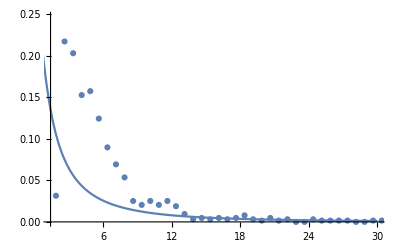

```mathematica
p1
```

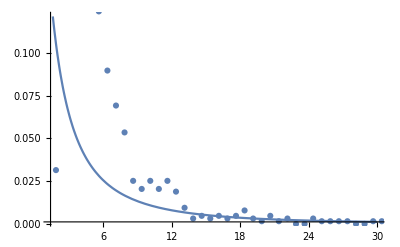

```mathematica
twoPlots=Show[Plot[(fitFunc)/.pV1,{x,1.6,30},PlotRange->{{1.4,30},Full}],ListPlot[kHist]]
```

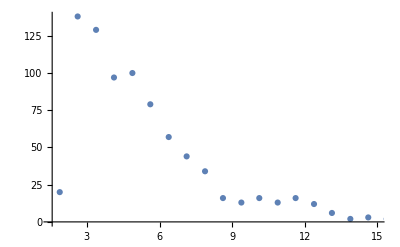

```mathematica
ListPlot[kHist,PlotRange->{{1.5,15},Full}]
```